Rongzhong Li
Feb. 13, 2013

# Cracking a Substitution Cipher

### Import Data and Frequency Analysis This is a long text. Shifts may happen at " " and "\n" during import. So it's not likely to be a transposition cypher. Notice during the import, the "\n" are deleted, and " " are transformed to "_" for better observation. Left and right quotes are both set to "\"".

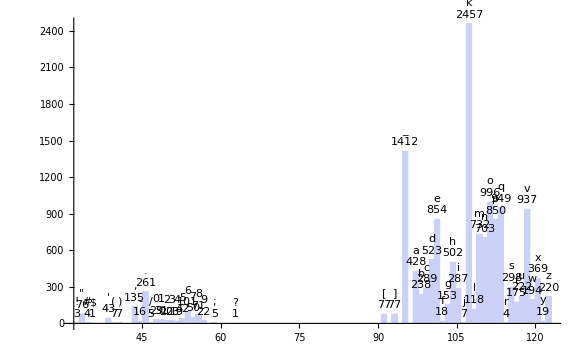

```mathematica
en0=Import[StringJoin[{NotebookDirectory[],"cipher.txt"}],"Text"];
en=StringReplace[en0,{"\n"..->"","“"->"\"","”"->"\"","–"->"-"," "->"_"}];
charcode=ToCharacterCode[en];(*translate to ASCII code*)
fromcode[s_]:=Table[FromCharacterCode[s[[i]]],{i,Length[s]}];
char=fromcode[charcode];
hist[group_]:=(labeler[v_,{i_,j_},{ri_,cj_}]:=Placed[{CharacterRange[FromCharacterCode[Min[group]],FromCharacterCode[Max[group]]][[j]],v},Above,Column];Histogram[group,Max[group]-Min[group]+1,LabelingFunction->labeler])
hist[charcode]
```

### The text is probably encrypted separately in the domain of letters and symbols. And considering the pairing citation braket units, the symbols should be uncoded. The numbers are often in brackets, so they should be encrypted within their domain. The text is probably an academic paper downloaded from some website.

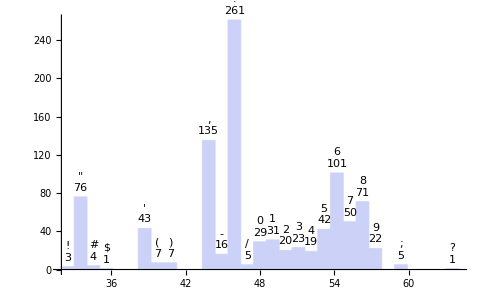

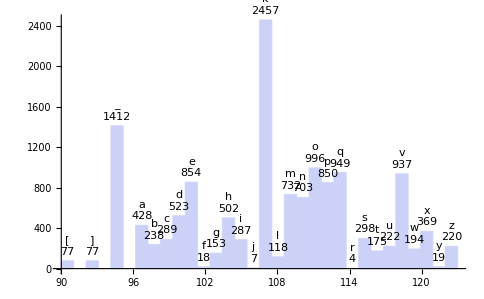

```mathematica
symbolcode={};lettercode={};
Table[If[charcode[[i]]<90,symbolcode=Append[symbolcode,charcode[[i]]],lettercode=Append[lettercode,charcode[[i]]]],{i,Length[charcode]}];
symbol=fromcode[symbolcode];letter=fromcode[lettercode];style={Bold,15,Blue};
hist[symbolcode]
hist[lettercode]
```

```mathematica
statistic[repeat_]:=(Tgram0=Tally[Table[StringJoin[Table[char[[i+r-1]],{r,repeat}]],{i,Length[char]-repeat}]];Tgram={};Table[If[
(repeat≥0&&repeat<2&&Tgram0[[i,2]]>200)||
(repeat==2&&Tgram0[[i,2]]>125)||
(repeat==3&&Tgram0[[i,2]]>50)||
(repeat==4&&repeat<5&&Tgram0[[i,2]]>35),
Tgram=Append[Tgram,Tgram0[[i]]]],{i,Length[Tgram0]}];Sort[Tgram,#1[[2]]>#2[[2]]&])
```

```mathematica
Print[Style["💡 Normal English:\n",style],Column[{MatrixForm[{{"e","t","r","n","i","o","a","s"}, {"th","he","in","er","an", "re", "nd", "at"}, {"the","and","tha","ion","ing", "ion","tio","for"},{"that","with","this","from","have","they","were","been"},{"which","their","there","","","","",""}}],MatrixForm[{{"Frequent:", "ss", "ll", "oo", "ee", "nn", "pp"}, {"Hardly:", "aa", "yy", "uu", "", "", ""}}]}]]
double={};Print[Style["💡 Text Statistics:\n",style],Column[Table[MatrixForm[Transpose[statistic[t]]],{t,4}]]]
Table[If[char[[i+1]]==char[[i]],double=Append[double,StringJoin[{char[[i]],char[[i]]}]]],{i,Length[char]-1}];
Print["Repeating: ",MatrixForm[Transpose[Tally[double]]]]
```

💡 Normal English:
(e | t | r | n | i | o | a | s
th | he | in | er | an | re | nd | at
the | and | tha | ion | ing | ion | tio | for
that | with | this | from | have | they | were | been
which | their | there |  |  |  |  | )
(Frequent: | ss | ll | oo | ee | nn | pp
Hardly: | aa | yy | uu |  |  | )

💡 Text Statistics:
(k | _ | o | q | v | e | p | m | n | d | h | a | x | s | c | i | . | b | u | z
2456 | 1412 | 996 | 949 | 937 | 854 | 850 | 732 | 703 | 523 | 502 | 428 | 369 | 298 | 289 | 287 | 261 | 238 | 222 | 220)
(_k | ko | kv | od | ep | d_ | nk | ak | _m | qp | pk | ok | kn | ku | kq | pc | mk | _a | vp | o_ | vn
403 | 355 | 286 | 282 | 268 | 258 | 243 | 210 | 202 | 192 | 189 | 164 | 160 | 150 | 149 | 144 | 142 | 139 | 135 | 128 | 126)
(kod | od_ | d_k | _ak | epc | pck | _mk | koq | kvk | oqk | qpk | kep | vnk | kqb | qbk | kvp | kvn | kuv | epk | ako | mex
239 | 205 | 192 | 117 | 115 | 107 | 86 | 85 | 84 | 84 | 73 | 71 | 69 | 64 | 59 | 58 | 53 | 52 | 52 | 51 | 51)
(kod_ | od_k | epck | koqk | kqbk | mexg | kmex | mqhh | kuvn | uvnk | kvpa | vpak | gmqh | xgmq | exgm
190 | 178 | 90 | 80 | 59 | 48 | 45 | 44 | 42 | 40 | 39 | 38 | 38 | 38 | 36)

Repeating: (kk | qq | hh | .. | mm | ll | pp | __ | 66 | xx | bb | oo | 77 | nn | ii | 88 | cc | aa | 00 | 11 | 99 | 22 | 33
5 | 47 | 93 | 12 | 13 | 4 | 30 | 32 | 40 | 9 | 10 | 16 | 6 | 16 | 5 | 1 | 4 | 3 | 1 | 1 | 1 | 1 | 1)

### Letter Decryption (Original letters are capitalized for convenience during decryption.) In any text, the character " " and e should be the most abundant. So "k" and " " are probably " " and "E". Then od_ is THE. Regenerate the text and frequency table step by step for next clues. TEnT is TEST. v as a single word should be A. uAS is WAS. Since p is not s then Ip is IN. xSx is CSC. THeS is THIS. Tq is TO. Ob is OF. INc is ING. Now we can move to the text and check some words. SOiETHING is SOMETHING. MOeE is MORE. COM.sTER SECsRITz is COMPUTER SECURITY. NUMwERS is NUMBERS. MAPPEa CORRECThYl is MAPPED CORRECTLY. So l should be ".". LOtES is LOVES. SPEAgER is SPEAKER. Now only J,Q,X,Z or f,j,r,y are not find. Search the text for f,j,r,y. fANUARY is JANUARY. MAGAjINE is MAGAZINE. rUESTION is Question. Then y is X.

```mathematica
Print[Style["💡 Codebook:\n",style],MatrixForm[(*Original letters are capitalized for convenience during decryption.*)codebook=({{"A", "B", "C", "D", "E", "F", "G", "H", "I", "J", "K", "L", "M", "N", "O", "P", "Q", "R", "S", "T", "U", "V", "W", "X", "Y", "Z", " ", "."}, {"v", "w", "x", "a", " ", "b", "c", "d", "e", "f", "g", "h", "i", "p", "q", ".", "r", "m", "n", "o", "s", "t", "u", "y", "z", "j", "k", "l"}})]]
codebookrule=Table[codebook[[2,i]]->codebook[[1,i]],{i,Dimensions[codebook][[2]]}];
deL=StringReplace[en0,codebookrule];
charcode=ToCharacterCode[deL];char=fromcode[charcode];
Print[Style["💡 Text Statistics:\n",style],Column[Table[MatrixForm[Transpose[statistic[t]]],{t,4}]]]
deL;
```

💡 Codebook:
(A | B | C | D | E | F | G | H | I | J | K | L | M | N | O | P | Q | R | S | T | U | V | W | X | Y | Z |   | .
v | w | x | a |   | b | c | d | e | f | g | h | i | p | q | . | r | m | n | o | s | t | u | y | z | j | k | l)

💡 Text Statistics:
(  | E | T | O | A | I | N | R | S | H | L | D | C | U | G | M | P | F | W | Y
2457 | 1412 | 996 | 949 | 937 | 854 | 850 | 732 | 703 | 523 | 502 | 428 | 369 | 298 | 289 | 287 | 261 | 238 | 222 | 220)
(E  |  T |  A | TH | IN | HE | S  | D  | ER | ON | N  | T  |  S |  W |  O | NG | R  | ED | AN | TE | AS
403 | 354 | 286 | 282 | 268 | 258 | 243 | 210 | 202 | 192 | 189 | 164 | 160 | 150 | 149 | 144 | 142 | 139 | 135 | 128 | 126)
( TH | THE | HE  | ED  | ING | NG  | ER  |  TO |  A  | TO  | ON  |  IN | AS  |  OF | OF  |  AN |  AS |  WA | IN  | D T | RIC
238 | 205 | 192 | 117 | 115 | 107 | 86 | 85 | 84 | 84 | 73 | 71 | 69 | 64 | 59 | 58 | 53 | 52 | 52 | 51 | 51)
( THE | THE  | ING  |  TO  |  OF  | RICK | ROLL |  RIC |  WAS | WAS  |  AND | AND  | KROL | CKRO | ICKR
189 | 178 | 90 | 80 | 59 | 48 | 44 | 44 | 42 | 40 | 39 | 38 | 38 | 38 | 36)

### Number Decryption According to the first paragraphs, 015/315->348/648, 7->1, 8670->2013, 7954->198?, 8665->2008. Citation index should go increasingly. So 2->5, 4->7. Then I can get (0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 6 | 7 | 8 | 0 | 1 | 2 | 3 | 4 | 5 | 9)

```mathematica
Print[Style["💡 Codebook:\n",style],MatrixForm[codebook=({{"0", "1", "2", "3", "4", "5", "6", "7", "8", "9"}, {"6", "7", "8", "0", "1", "2", "3", "4", "5", "9"}})]]
codebookrule=Table[codebook[[2,i]]->codebook[[1,i]],{i,Dimensions[codebook][[2]]}];
deN=StringReplace[deL,codebookrule]
```

💡 Codebook:
(0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9
6 | 7 | 8 | 0 | 1 | 2 | 3 | 4 | 5 | 9)

CSC 348/648  COMPUTER SECURITY  648 TEST 1  SPRING 2013
WOOOOOOOOOOOOOOOOOOOO, YOU BROKE THIS ONE! WELL DONE. PERHAPS! I HOPE YOU CAN GET ALL THE NUMBERS MAPPED CORRECTLY.

NOW ON TO SOMETHING MORE INTERESTING, A SINGER DIGITAL BEAR TRULY LOVES... YO, EMILY, WHY NOT GET RICK ASTELY AS A SPEAKER FOR ACM, INSTEAD OF SOME DENTIST WHO BREAKS HIS RIBS!  

RICKROLLING IS AN INTERNET MEME[1][2] INVOLVING THE MUSIC VIDEO FOR THE 1987 RICK ASTLEY SONG "NEVER GONNA GIVE YOU UP". THE MEME IS A BAIT AND SWITCH; A PERSON PROVIDES A HYPERLINK SEEMINGLY RELEVANT TO THE TOPIC AT HAND, BUT ACTUALLY LEADS TO ASTLEY'S VIDEO. THE LINK CAN BE MASKED OR OBFUSCATED IN SOME MANNER SO THAT THE USER CANNOT DETERMINE THE TRUE DESTINATION OF THE LINK WITHOUT CLICKING. PEOPLE LED TO THE MUSIC VIDEO ARE SAID TO HAVE BEEN RICKROLLED. RICKROLLING HAS EXTENDED BEYOND WEB LINKS TO PLAYING THE VIDEO OR SONG DISRUPTIVELY IN OTHER SITUATIONS, INCLUDING PUBLIC PLACES,[2] SUCH AS A LIVE APPEARANCE OF ASTLEY HIMSELF IN THE 2008 MACY'S THANKSGIVING DAY PARADE IN NEW YORK.[1] THE MEME HAS HELPED TO REVIVE ASTLEY'S CAREER.[3]

HISTORY
ASTLEY RECORDED "NEVER GONNA GIVE YOU UP" ON HIS 1987 ALBUM WHENEVER YOU NEED SOMEBODY.[4] THE SONG, HIS SOLO DEBUT SINGLE, WAS A NUMBER ONE HIT ON SEVERAL INTERNATIONAL CHARTS, INCLUDING THE BILLBOARD HOT 100, HOT ADULT CONTEMPORARY TRACKS AND UK SINGLES CHART. AS A MEANS OF PROMOTING THE SONG, IT WAS ALSO MADE INTO ASTLEY'S FIRST MUSIC VIDEO, WHICH FEATURES HIM PERFORMING THE SONG WHILE DANCING.[5]

RICKROLLING IS SAID TO HAVE BEGUN AS A VARIANT OF AN EARLIER PRANK FROM THE IMAGEBOARD 4CHAN KNOWN AS DUCKROLLING,[6] IN WHICH A LINK TO SOMEWHERE (SUCH AS A SPECIFIC PICTURE OR NEWS ITEM) WOULD INSTEAD LEAD TO A THREAD OR SITE CONTAINING AN EDITED PICTURE OF A DUCK WITH WHEELS. THE USER AT THAT POINT IS SAID TO HAVE BEEN "DUCKROLLED".

THE FIRST KNOWN INSTANCE OF A RICKROLL OCCURRED IN MAY 2007 ON /V/, 4CHAN'S VIDEO GAME BOARD, WHERE A LINK TO THE RICK ASTLEY VIDEO WAS CLAIMED TO BE A MIRROR OF THE FIRST TRAILER FOR GRAND THEFT AUTO IV (WHICH WAS UNAVAILABLE DUE TO HEAVY TRAFFIC). THE JOKE WAS CONFINED TO 4CHAN FOR A VERY BRIEF PERIOD.[6]

BY MAY 2008,[7] THE PRACTICE HAD SPREAD BEYOND 4CHAN AND BECAME AN INTERNET PHENOMENON, EVENTUALLY ATTRACTING COVERAGE IN THE MAINSTREAM MEDIA.[2][8][9] AN APRIL 2008 POLL BY SURVEYUSA ESTIMATED THAT AT LEAST 18 MILLION AMERICAN ADULTS HAD BEEN RICKROLLED.[10] IN SEPTEMBER 2009, WIRED MAGAZINE PUBLISHED A GUIDE TO MODERN HOAXES WHICH LISTED RICKROLLING AS ONE OF THE BETTER KNOWN BEGINNER-LEVEL HOAXES, ALONGSIDE THE FAKE E-MAIL CHAIN LETTER.[11]

THE ORIGINAL VIDEO ON YOUTUBE USED FOR RICKROLLING WAS REMOVED FOR TERMS OF USE VIOLATIONS IN FEBRUARY 2010[12] BUT WAS REPOSTED WITHIN A DAY.[13]  

EXAMPLES
EWU BASKETBALL GAMES
FOUR WOMEN'S BASKETBALL GAMES AT EASTERN WASHINGTON UNIVERSITY (EWU) WERE RICKROLLED DURING MARCH 2008. BEFORE THE START OF THE GAMES, "NEVER GONNA GIVE YOU UP" WAS PLAYED WHILE A RICK ASTLEY IMPERSONATOR DANCED AND LIP-SYNCHED TO THE MUSIC. A VIDEO CONTAINING FOOTAGE OF THE PRE-GAME RICKROLLINGS, MISLEADINGLY COMBINED WITH REAL GAME BREAK FOOTAGE, WAS LATER RELEASED ON YOUTUBE.[2][17] 

THE NEW YORK TIMES ORIGINALLY REPORTED THAT A SINGLE GAME HAD ACTUALLY BEEN INTERRUPTED BY THE RICKROLLING. ON 27 MARCH 2008 IT ISSUED A CORRECTION CLARIFYING THE SITUATION, AND SAYING THAT THE INTERRUPTION NEVER TOOK PLACE, BUT WAS RATHER A HOAX BY PAWL FISHER, A STUDENT; DAVIN PERRY, WHO SHOOTS GAME VIDEOS FOR THE UNIVERSITY; AND DAVE COOK, THE UNIVERSITY'S SPORTS INFORMATION DIRECTOR.[2][17][18][19][20][21]

NEW YORK METS
ON 4 APRIL 2008, MANY WEB COMMUNITIES, STARTING WITH FARK.COM,[22] URGED THEIR READERS TO VOTE "NEVER GONNA GIVE YOU UP" FOR THE 8TH INNING SING-ALONG AT SHEA STADIUM FOR THE NEW YORK METS SEASON. THE METS POSTED A WEB POLL TO SELECT A SONG, AND LEFT A BLANK FIELD FOR WRITE-INS. THE METS ORGANIZATION ANNOUNCED ON 7 APRIL 2008 THAT "NEVER GONNA GIVE YOU UP" WAS THE WINNER WITH MORE THAN FIVE MILLION VOTES.[23] THE METS DECIDED NOT TO COMMIT TO USING ASTLEY'S SONG AND SUBSEQUENTLY ANNOUNCED A RUN-OFF AMONG SIX SONGS THAT WOULD BE PLAYED AT SHEA STADIUM FOR THE NEXT SIX GAMES, STARTING WITH "NEVER GONNA GIVE YOU UP" ON 8 APRIL 2008.[24]
MLB.COM LATER REPORTED ON THE GAME, CLAIMING "NEVER GONNA GIVE YOU UP" WAS PLAYED AS A "RESULT OF FANS RIGGING THE VOTE IN FAVOR OF ASTLEY, ALL PART OF A UNIVERSAL INTERNET PHENOMENON KNOWN AS RICK ROLLING". THE SONG WAS PLAYED DURING THE HOME OPENER AND WAS GREETED WITH "A SHOWER OF BOOS".[25]

APRIL FOOLS' DAY, 2008
ON APRIL FOOLS' DAY 2008 AND THE FOLLOWING WEEKS, NUMEROUS SEEMINGLY UNCOORDINATED INSTANCES OF RICKROLLING APPEARED ON THE INTERNET, AND NEWS MEDIA. ALL OF THE FEATURED VIDEOS ON YOUTUBE'S FRONT PAGE HYPERLINKED TO THE RICKROLL. THE PRANK BEGAN WITH INTERNATIONAL YOUTUBE PORTALS BEFORE APPEARING ON THE MAIN SITE.[26]
SOCIAL BLOG WEBSITE LIVEJOURNAL ANNOUNCED ON THE SAME DAY THAT THEY WOULD BE ADDING A NEW MEMBER TO THEIR ADVISORY BOARD, LINKING MEMBERS TO THE JOURNAL "RICKASTLEY", WHICH CONTAINS A RICKROLL.[27]
THE WEBSITE FARK FEATURED A LINK TO A VIDEO CLAIMING TO BE A BLOOPER REEL FOR THE MUPPETS BUT INSTEAD LINKED TO A VIDEO OF BEAKER PERFORMING RICK ASTLEY'S SONG (TO A VIDEO OF HIM ORIGINALLY PERFORMING "FEELINGS" ON THE MUPPET SHOW).[28] OTHER SOCIAL BOOKMARKING SITES SUCH AS DIGG[29] AND REDDIT[CITATION NEEDED] SUBSEQUENTLY JOINED IN LINKING THE VIDEO.
THE ONLINE WEB STORE THINKGEEK ADVERTISED ON THEIR FRONT PAGE A BETAMAX TO HD DVD CONVERTER DEVICE. IN THE PRODUCT PAGE A DEMONSTRATION VIDEO WAS LINKED WHICH WAS, IN ACTUALITY, A RICKROLL.[30]

DAN KAMINSKY
IN APRIL 2008, SECURITY EXPERT DAN KAMINSKY DEMONSTRATED A SERIOUS SECURITY VULNERABILITY BY SETTING UP RICKROLLS ON FACEBOOK AND PAYPAL.[31]

MICHELLE OBAMA
ON 7 JUNE 2008, A NUMBER OF POLITICAL BLOGS, INCLUDING WONKETTE,[32] ANDREW SULLIVAN,[33] AND BALLOON JUICE,[34] POSTED AN ARTICLE CLAIMING TO SHOW MICHELLE OBAMA GOING ON A RANT FULL OF RACIST REFERENCES TO "WHITEY", BUT THE VIDEO WAS ACTUALLY A RICKROLL.

BARACK ROLL
HUGH ATKIN, AN AUSTRALIAN LAWYER AND NOTABLE PRODUCER OF INTERNET VIRAL VIDEOS,[35] CREATED A POPULAR YOUTUBE PARODY VIDEO OF THE RICKROLLING MEME INVOLVING U.S. PRESIDENT BARACK OBAMA, THE THEN 2008 PRESIDENTIAL CANDIDATE FOR THE DEMOCRATIC PARTY, AND A SENATOR FROM ILLINOIS, ENTITLED "BARACK ROLL" THAT HAS BEEN WATCHED ABOUT 6 MILLION TIMES SINCE ITS RELEASE. THE ORIGINAL VIDEO HAS SINCE BEEN MUTED DUE TO AN UNAUTHORIZED SOUNDTRACK,[36] ALTHOUGH, AS USUAL IN SUCH CASES, MANY COPIES OF THE VIDEO HAVE BEEN RE-UPLOADED BY OTHER USERS. THE VIDEO CONSISTS OF CLIPS OF OBAMA SPEAKING THE WORDS OF ASTLEY'S SONG AND SCENES OF HIS APPEARANCE ON THE ELLEN DEGENERES SHOW. A FOLLOW-UP VIDEO SHOWS SENATOR JOHN MCCAIN BEING "BARACK ROLLED" AT THE REPUBLICAN NATIONAL CONVENTION, THOUGH IT NEVER HAPPENED; THE "BARACK ROLL" IMAGE WAS DISPLAYED ON THE GIANT BLUE SKY BACKGROUND THAT WAS BEHIND JOHN MCCAIN DURING PARTS OF HIS SPEECH, AND THE VIDEO WAS PIECED TOGETHER FROM FOOTAGE OF THE EVENT. THE VIDEO ENDS WITH WHAT LOOKS LIKE THE DELEGATION CHEERING WHILE CHANTING OBAMA'S NAME.[37] THIS VERSION WON THE FAVORITE USER GENERATED VIDEO AWARD AT THE 35TH PEOPLE'S CHOICE AWARDS.
IT WAS HIGHLIGHTED ON BLOGS FOR THE NEW YORK TIMES,[38] THE POLITICO,[39] COMEDY CENTRAL,[40] ANDREW SULLIVAN[41] AND SPORTS ILLUSTRATED.[42] WRITING FOR TIME MAGAZINE'S 2009 TIME 100 ISSUE, ASTLEY HIMSELF MENTIONED THE VIDEO IN HIS WRITEUP FOR 4CHAN FOUNDER MOOT.[43]

2008 MACY'S THANKSGIVING DAY PARADE
ON 27 NOVEMBER 2008, ASTLEY PARTICIPATED IN A LIVE RICKROLL DURING THE MACY'S THANKSGIVING DAY PARADE WHILE THE FOSTER'S HOME FOR IMAGINARY FRIENDS CHARACTERS WERE SINGING "BEST FRIEND", THE THEME FROM THE 1970S TV SERIES THE COURTSHIP OF EDDIE'S FATHER. MIDWAY THROUGH THE SONG, ASTLEY EMERGED FROM THE FLOAT AND BEGAN TO LIP SYNC HIS SIGNATURE HIT FOR THE CROWD. AT THE END OF ASTLEY'S PERFORMANCE, CHEESE (A CHARACTER FROM FOSTER'S) SHOUTED OUT "I LIKE RICKROLLING?"[44]

2008 CHRISTMAS FACEBOOK CAMPAIGN
ALSO KNOWN AS THE "ULTIMATE RICKROLL".
ON 1 DECEMBER 2008, A CAMPAIGN WAS STARTED ON FACEBOOK IN AN ATTEMPT TO MAKE THE SONG THE 2008 CHRISTMAS #1 IN THE UK AS AN ATTEMPT TO "RICKROLL" THE COUNTRY DURING CHRISTMAS. THE CAMPAIGN'S PURPOSE WAS TO STOP THE X-FACTOR FROM GAINING THE #1 CHRISTMAS SPOT, THEREBY ENDING THE SHOW'S CHAIN OF SUCCESS. THE GROUP ATTRACTED NEARLY 30,000 PEOPLE IN ITS FIRST WEEK ACTIVE. CAMPAIGNERS WERE ENCOURAGED TO GET AS MANY PEOPLE AS POSSIBLE TO DOWNLOAD THE SONG FROM ITUNES BETWEEN 15 AND 20 DECEMBER 2008. THE SONG ONLY MANAGED TO PEAK AT #73; HOWEVER, THIS WAS LATER FOUND TO BE A DELIBERATE LOWERING OF THE SONG'S PLACE (HAVING REACHED #3 A WEEK BEFORE IT CAME TO ITS FINISH) DUE TO THE COMPANY'S BELIEF THAT "THE SONGS [SIC] RANKING WAS RIDICULOUS AND RIGGING A CONTEST WAS UNFAIR ON OTHER ARTISTS".[45][NOT IN CITATION GIVEN] THE CAMPAIGNERS, JON AND TRACY MORTER, WERE ULTIMATELY SUCCESSFUL THE FOLLOWING YEAR WITH A RAGE AGAINST THE MACHINE CAMPAIGN FOR THE 1992 SONG "KILLING IN THE NAME" THAT HIT THE NO.1 SPOT IN DECEMBER 2009.

NANCY PELOSI
ON 13 JANUARY 2009, IN HONOR OF THE NEW YOUTUBE HUB FOR CONGRESS, U.S. SPEAKER OF THE HOUSE NANCY PELOSI UPLOADED A VIDEO CALLED "SPEAKER PELOSI PRESENTS CAPITOL CAT CAM" TO HER OFFICIAL YOUTUBE CHANNEL. SHE DESCRIBED IT AS "A BEHIND THE SCENES VIEW OF THE SPEAKER'S OFFICE IN THE U.S. CAPITOL". THE VIDEO DEPICTS CATS ROAMING AROUND THE OFFICE. A RICKROLL OCCURS APPROXIMATELY HALFWAY THROUGH THE VIDEO.[46]

IPHONE WORM
IN OCTOBER/NOVEMBER 2009, A WORM DESIGNED TO INFECT JAILBROKEN IPHONES CHANGED THE WALLPAPER OF INFECTED PHONES TO A PICTURE OF RICK ASTLEY OVERLAID WITH THE TEXT "IKEE IS NEVER GOING TO GIVE YOU UP".[47]

OREGON HOUSE OF REPRESENTATIVES
IN FEBRUARY 2010, A BIPARTISAN GROUP OF OREGON REPRESENTATIVES CONSPIRED TO DO A PHANTOM RICKROLL DURING HOUSE SESSIONS. EACH OF THE CONSPIRATORS WAS GIVEN A PORTION OF THE LYRICS OF NEVER GONNA GIVE YOU UP TO WORK UNOBTRUSIVELY INTO THEIR STATEMENTS DURING LEGISLATIVE DISCUSSION. THIS SCHEME WAS FINALLY REVEALED ON APRIL 1, 2011, WHEN A VIDEO, EDITED BY REPRESENTATIVE JEFFERSON SMITH AND HIS CO-CONSPIRATORS, WAS RELEASED OF THE VARIOUS REPRESENTATIVES MAKING THEIR STATEMENTS, PUT IN PROPER LYRICAL ORDER.[48]

WHITE HOUSE TWITTER FEED
ON 27 JULY 2011 OFFICIALS MANAGING THE WHITE HOUSE TWITTER FEED RESPONDED TO A MESSAGE THAT THE FEED WAS DULL, WRITING "SORRY TO HEAR THAT. FISCAL POLICY IS IMPORTANT, BUT CAN BE DRY SOMETIMES. HERE'S SOMETHING MORE FUN," FOLLOWED BY A LINK TO NEVER GONNA GIVE YOU UP.[49]

CSC 348/648 RICKROLL
IT SEEMS THAT FULP CONSTANTLY ENJOYS RICKROLLIN' HIS CLASS, WEIRD... WELL THE CLASS BETTER GET USED TO IT CAUSE IT GONNA HAPPEN OVER AND OVER AND OVER AND OVER. IF YOU HAVE READ THIS FAR, WELL THEN THIS SHOULD HELP 0123456789.

OTHERS
A RICKROLL FLASH MOB TOOK PLACE ON 11 APRIL 2008, IN LONDON'S LIVERPOOL STREET TRAIN STATION WITH AN ESTIMATED 300–400 PEOPLE IN ATTENDANCE.[50][51] WHEN THE FLASH MOB FINISHED THE COUNTDOWN, THEY SANG THE SONG FROM BEGINNING TO END.
ONE WEB SITE, PRANKDIALER.COM,[52] OFFERS A RICKROLL-BY-PHONE SERVICE, ALLOWING VISITORS TO ENTER A PHONE NUMBER TO BE CALLED AND HAVE THE SONG PLAYED TO THE ANSWERING PARTY.[53]
THE MIT DOME WAS HACKED ON SEPTEMBER 9, 2009, TO SHOW A GIANT SET OF THE FIRST NOTES OF "NEVER GONNA GIVE YOU UP".[54]
AS PART OF PROMOTION FOR THEIR TITLE DANTE'S INFERNO, ELECTRONIC ARTS SENT WOODEN BOXES TO SEVERAL VIDEO GAME WEBSITES, INCLUDING THE ESCAPIST, DESTRUCTOID AND CHUD.COM. EACH BOX CONTAINED A HAMMER AND A PAIR OF GOGGLES, AND WHEN OPENED, THE BOX WOULD PLAY THE RICK ASTLEY SONG ON A CONTINUOUS LOOP. THE ONLY WAY TO STOP IT WAS TO DESTROY IT. AFTER DOING SO, THE RECIPIENT WOULD THEN FIND A SCROLL CLAIMING THAT HE OR SHE WAS DAMNED TO HELL FOR COMMITTING THE SIN OF WRATH.[55][56][57]
MICROSOFT DEALT WITH PEOPLE ABUSING THE FREE WI-FI AT ITS 2009 BRISBANE TECHED CONFERENCE WITH BITTORRENTING[58] BY REDIRECTING LOCAL DNS RESULTS FOR THE TOP BITTORRENT TRACKERS TO A LOCAL WEB SERVER CONTAINING SOME RICKROLL SCRIPTS.[59][60]
IN MAY 2008, THERE WAS A FLASHMOB IN BALTIMORE INNER HARBOR WHICH INCLUDED 50 PEOPLE SINGING "NEVER GONNA GIVE YOU UP".[61]
GOOGLE.COM'S GOOGLE LABS BOOK NGRAM VIEWER, A PHRASE-TRENDING GRAPH OF SEARCHED TERMS, DISPLAYS THE YOUTUBE VIDEO IF THE TERM "NEVER GONNA GIVE YOU UP" IS SEARCHED FOR.[62]
ON THE 29 JULY 2011 EPISODE OF THE BRITISH GAMESHOW POINTLESS, THERE WAS A QUESTION ABOUT THE SONG. IN THE SECOND QUESTION OF THE THIRD ROUND, TWO TEAMS TRIED TO GUESS ONE OF SIX THINGS RICK ASTLEY IS "NEVER GONNA DO".
ON 11 JANUARY 2012, THE OCCUPY PITTSBURGH MOVEMENT SAID THEY WILL PLAY "NEVER GONNA GIVE YOU UP" IF CONFRONTED BY AUTHORITIES.[63]
IN THE FM (TV SERIES), IN THE END OF THE FIRST EPISODE, CHRIS O'DOWD'S CHARACTER, WHILE PRETENDING TO BE A SKILLFUL DJ AND FAILING, ACCIDENTALLY RICKROLLS THE CROWD IN THE CLUB IN WHICH HE IS PERFORMING.

EFFECTS ON ASTLEY AND REACTION
IN A MARCH 2008 INTERVIEW, ASTLEY SAID THAT HE FOUND THE RICKROLLING OF FULP'S CLASSES TO BE "HILARIOUS" AND IN 2013 HE WANTED TO BE A SPEAKER AT WAKE FOREST, BUT A DENTIST WITH BROKEN RIBS WAS SELECTED OVER HIM. HE ALSO SAID THAT HE WILL NOT TRY TO CAPITALIZE ON THE RICKROLL PHENOMENON WITH A NEW RECORDING OR REMIX OF HIS OWN, BUT THAT HE WOULD BE HAPPY TO HAVE OTHER ARTISTS REMIX IT. OVERALL, ASTLEY IS NOT TROUBLED BY THE PHENOMENON, STATING THAT HE FINDS IT "BIZARRE AND FUNNY" AND THAT HIS ONLY CONCERN IS THAT HIS "DAUGHTER DOESN'T GET EMBARRASSED ABOUT IT".[64] A SPOKESPERSON FOR ASTLEY'S RECORD LABEL RELEASED A COMMENT WHICH SHOWED THAT ASTLEY'S INTEREST WITH THE PHENOMENON HAD FADED, AS THEY STATED "I'M SORRY, BUT HE'S DONE TALKING ABOUT RICKROLLING".[6] SIMPLY PUT, HE ONLY WANTED TO PERSONALLY RICKROLL WAKE FOREST, BUT EMILY SAID NO. EMILY CRUSHED HIS ONLY WISH, WAY TO GO EMILY. WE HOPE YOU ARE HAPPY, CAUSE RICK AIN'T.

IN NOVEMBER 2008, RICK ASTLEY WAS NOMINATED FOR "BEST ACT EVER" AT THE MTV EUROPE MUSIC AWARDS AFTER THE ONLINE NOMINATION FORM WAS FLOODED WITH VOTES.[65] THE PUSH TO MAKE ASTLEY THE WINNER OF THE AWARD CONTINUED AFTER THE ANNOUNCEMENT, AS WELL AS EFFORTS TO ENCOURAGE MTV TO PERSONALLY INVITE ASTLEY TO THE AWARDS CEREMONY.[66] ON 10 OCTOBER ASTLEY'S WEBSITE CONFIRMED THAT AN INVITATION TO THE AWARDS HAD BEEN RECEIVED. ON 6 NOVEMBER 2008, JUST HOURS BEFORE THE CEREMONY WAS DUE TO AIR, IT WAS REPORTED THAT MTV EUROPE DID NOT WANT TO GIVE ASTLEY THE AWARD AT THE CEREMONY, INSTEAD WANTING TO PRESENT IT AT A LATER DATE. MANY FANS WHO VOTED FOR ASTLEY FELT THE AWARDS CEREMONY FAILED TO ACKNOWLEDGE HIM AS A LEGITIMATE ARTIST. ASTLEY STATED IN AN INTERVIEW THAT HE FELT THE AWARD WAS "DAFT", BUT NOTED THAT HE THOUGHT THAT "MTV WERE THOROUGHLY RICKROLLED", AND WENT ON TO THANK EVERYONE WHO VOTED FOR HIM.[67]
IN 2009, ASTLEY WROTE ABOUT 4CHAN FOUNDER MOOT FOR TIME MAGAZINE'S ANNUAL TIME 100 ISSUE, WHERE HE THANKED MOOT FOR THE RICKROLLING PHENOMENON.[43]
ACCORDING TO THE REGISTER, HOWEVER, ASTLEY HAS ONLY DIRECTLY MADE $12, IN PERFORMANCE ROYALTIES FROM YOUTUBE, FROM THE MEME.[68]